# Bridge@Lofting

### 基本放样

```mathematica
bridge[l1_,l2_,u_]:=ParametricPlot3D[{v l1+(1-v)l2},u,{v,0,1},AxesLabel->{x,y,z}]
bridge[{Cos[θ],Sin[θ],0},{0.5Cos[θ],1.2Sin[θ],1},{θ,0,2π}]
```

-Graphics3D-

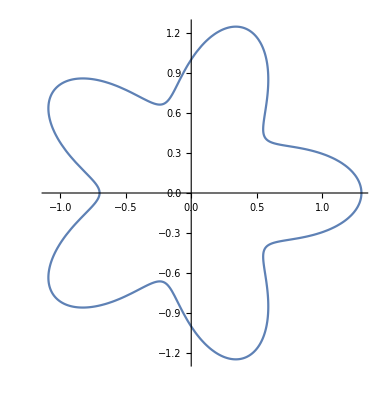

```mathematica
flower[θ_,n_:5]:={Cos[θ],Sin[θ]}(1+0.3Cos[n θ])
ParametricPlot[flower[θ],{θ,0,2π}]
```

```mathematica
bridge[{Cos[θ],Sin[θ],0},Append[flower[θ],1],{θ,0,2π}]
```

-Graphics3D-

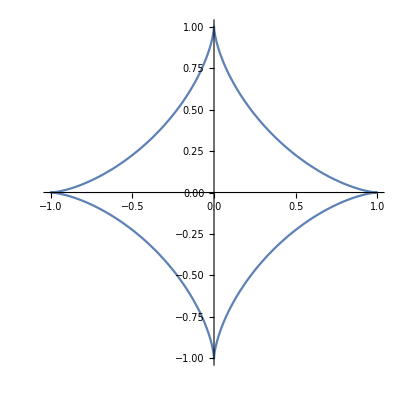

```mathematica
astroid=PlaneCurveData["Astroid","ParametricEquations"][1];
ParametricPlot[astroid[x],{x,0,2π}]
```

```mathematica
bridge[Append[astroid[θ],0],Append[flower[θ,4],1],{θ,0,2π}]
```

-Graphics3D-

```mathematica
Append
```

-Graphics-